```mathematica
DateListPlot[FinancialData["MSFT",All]]
```

```mathematica
ChemicalData["Rapamycin"]
```

```mathematica
GraphicsGrid[Partition[ListLogPlot[Table[ElementData[z,#],{z,108}],Joined->True,Filling->Axis,Frame->True,FrameTicks->None,PlotLabel->ElementData[1,#,"Description"]]&/@{"AtomicRadius","BoilingPoint","CrustAbundance","Density","ElectricalConductivity","Electronegativity","FusionHeat","MeltingPoint","NeutronCrossSection","Resistivity","SoundSpeed","SpecificHeat","ThermalConductivity","UniverseAbundance","VaporizationHeat"},3]]
```

```mathematica
Column[Text/@WordData["red","Definitions","List"],ItemSize->{30,Automatic},Frame->All,Spacings->2,Background->LightYellow]
```

red color or pigment; the chromatic color resembling the hue of blood
emotionally charged terms used to refer to extreme radicals or revolutionaries
the amount by which the cost of a business exceeds its revenue
characterized by violence or bloodshed
of a color at the end of the color spectrum (next to orange); resembling the color of blood or cherries or tomatoes or rubies
(especially of the face) reddened or suffused with or as if with blood from emotion or exertion

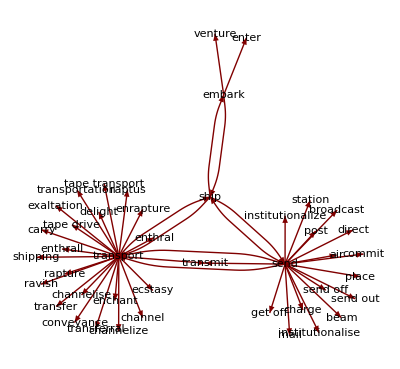

```mathematica
GraphPlot[Flatten[Rest[NestList[Union[Flatten[Thread[#->WordData[#,"Synonyms","List"]]&/@Last/@#]]&,{""->"ship"},2]]],VertexLabeling->True,DirectedEdges->True]
```

```mathematica
GraphicsGrid[Partition[GraphData/@GraphData["CayleyGraph"],7]]
```

-Graphics-

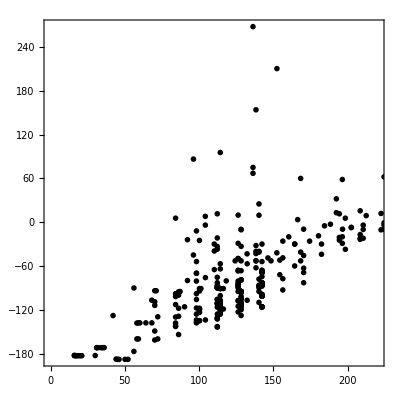

```mathematica
Graphics[Inset[ChemicalData[#],{ChemicalData[#,"MolecularWeight"],ChemicalData[#,"MeltingPoint"]},Center,Scaled[{.05,.05}]]&/@Select[ChemicalData["Alkane"],NumericQ[ChemicalData[#,"MeltingPoint"]]&],PlotRange->{{0,220},Automatic},Frame->True,AspectRatio->1]
```

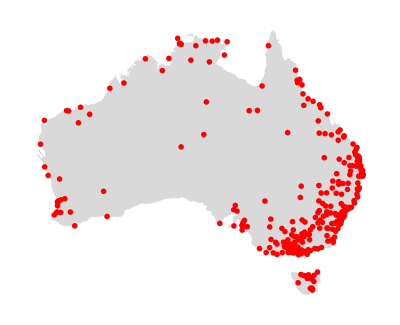

```mathematica
Graphics[{LightGray,CountryData["Australia","Polygon"],Red,PointSize[.01],Select[Point[Reverse[CityData[#,"Coordinates"]]]&/@CityData[{All,"Australia"}],FreeQ[#,_Missing]&]}]
```

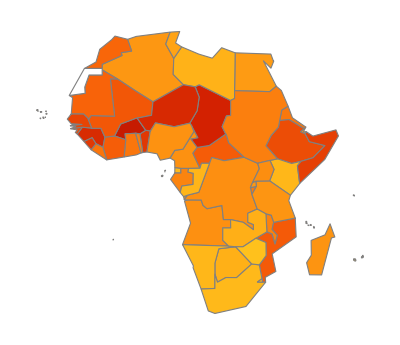

```mathematica
Graphics[{EdgeForm[Gray],Catch[ColorData["SolarColors"][CountryData[#,"LiteracyFraction"]/._Missing:>Throw[White]]],CountryData[#,"SchematicPolygon"]}&/@CountryData["Africa"]]
```

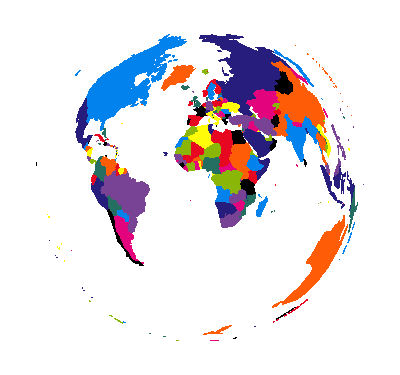

```mathematica
Graphics[MapIndexed[{ColorData[3][First[#2]],CountryData[#,{"SchematicPolygon","LambertAzimuthal"}]}&,CountryData[]]]
```

```mathematica
AstronomicalData[#,"Image"]&/@AstronomicalData["Planet"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DateListPlot[FinancialData[#,"Jan. 1, 2004"]&/@FinancialData["NYSE:AA*","Lookup"],Filling->Axis,Joined->True]
```

```mathematica
Play[Sum[Sin[1000 Sqrt[n] t (1+Cos[n t])],{n,10}],{t,0,2}]
```

-Graphics-

```mathematica
Sound[{SoundNote["G"],SoundNote["G"],SoundNote["G"],SoundNote["Eb",4]},1.5]
```

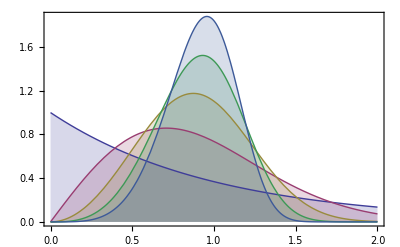

```mathematica
Plot[Evaluate[Table[PDF[WeibullDistribution[α,1]][x],{α,5}]],{x,0,2},Filling->Axis,Frame->True]
```

```mathematica
ExpectedValue[x^2/(1+x^4),ChiSquareDistribution[ν],x]
```

1/(ν/2)2^(-ν/2-2) (2^(ν/2) ν/2-2 _1 F_4(1;3/4-ν/8,1-ν/8,5/4-ν/8,3/2-ν/8;-1/4096)-2 π cos(1/(2 √2)) sinh(1/(2 √2)) cos((π ν)/8) sec((π ν)/4)+π cos(1/(2 √2)) cosh(1/(2 √2)) sec((π ν)/8)+π sin(1/(2 √2)) sinh(1/(2 √2)) sin((π ν)/8) sec((π ν)/4)-2 π sin(1/(2 √2)) cosh(1/(2 √2)) sin((π ν)/8) sec((π ν)/4)-π sin(1/(2 √2)) sinh(1/(2 √2)) cos((π ν)/8) cot((π ν)/8) sec((π ν)/4))

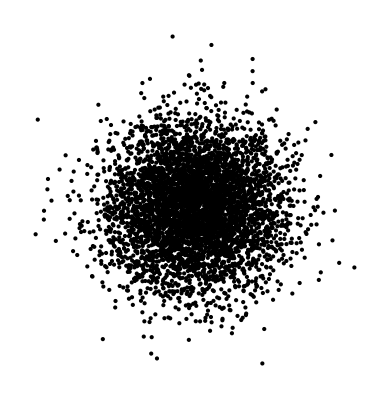

```mathematica
Graphics[Point[RandomReal[NormalDistribution[],{5000,2}]]]
```

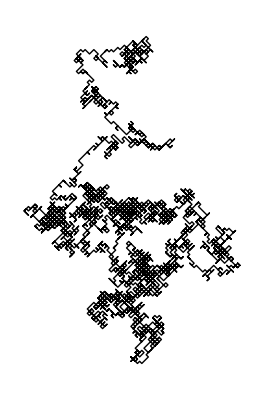

```mathematica
Graphics[Line[Accumulate[RandomChoice[{-1,1},{5000,2}]]]]
```

```mathematica
Plot3D[Evaluate[Total[Log[Map[PDF[GammaDistribution[α,β],#]&,RandomReal[GammaDistribution[2,10],50]]]]],{α,0.5,5},{β,2,25},MeshFunctions->{#3&},ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
Manipulate[Graphics[{Opacity[.75,Red],Table[Disk[Sqrt[i] {Sin[i (a Degree)],Cos[i (a Degree)]},size],{i,0,n}]},PlotRange->Sqrt[n]+size],{{n,100,"number of disks"},1,300},{{size,.75,"radius of disks"},0.1,2},{{a,137.5,"angle"},0,180,Appearance->"Labeled"}]
```

```mathematica
Manipulate[With[{w=CellularAutomaton[{n,{2,1},{1,1}},{{{1}},0},{{{t}}}]},ArrayPlot[ArrayFlatten[Table[w,{nt},{nt}]],ColorRules->{0->Purple,1->Red},Frame->False]],{{n,2,"rule number"},2,200,4},{{t,20,"number of steps"},1,90,1},{{nt,4,"number of tiles"},1,5,1},ControllerLinking->True]
```

```mathematica
Manipulate[Graphics[Line/@NestList[Flatten[#/.g[a_,b_]:>(g[b,b+(b-a) #]&/@{x+I y,1/2,x-I y})]&,g[0,1],t]/.g[a_,b_]:>{{Re[a],Im[a]},{Re[b],Im[b]}},PlotRange->All,ImageSize->{500,400}],{{x,0,"horizontal offset"},0,1},{{y,.5,"vertical offset"},0,1},Delimiter,{{t,6,"number of steps"},1,8,1}]
```

```mathematica
Manipulate[Graphics[{Opacity[.4,Red],Polygon[p[[Last[FindShortestTour[p]]]]]},PlotRange->1],{{p,RandomReal[{-1,1},{15,2}]},{-1,-1},{1,1},Locator}]
```

```mathematica
Manipulate[DateListPlot[FinancialData["^DJI",DatePlus[DateList[],{-n,"Day"}]],Joined->True,Filling->Bottom],{n,30,3000,1}]
```

```mathematica
{Slider[],Slider2D[],ColorSlider[Yellow],Button["Button"],ProgressIndicator[.3]}
```

{,,1,Button,}

```mathematica
Table[Slider[Mod[1.7 i,1]],{i,30}]
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
Column[{Slider[],Slider2D[],ColorSlider[],InputField[],Checkbox[],SetterBar[4,Range[10]],CheckboxBar[{1,3},Range[4]],RadioButtonBar[2,Range[5]],PopupMenu[a,{a,b,c}],Animator[],Manipulator[],ProgressIndicator[.6],Button["button"]}]
```

0.7









button

```mathematica
Panel[Grid[Table[Button[x^i+y^j],{i,10},{j,6}],Background->{{{LightRed,LightYellow}}}]]
```

x+y | x+y^2 | x+y^3 | x+y^4 | x+y^5 | x+y^6
x^2+y | x^2+y^2 | x^2+y^3 | x^2+y^4 | x^2+y^5 | x^2+y^6
x^3+y | x^3+y^2 | x^3+y^3 | x^3+y^4 | x^3+y^5 | x^3+y^6
x^4+y | x^4+y^2 | x^4+y^3 | x^4+y^4 | x^4+y^5 | x^4+y^6
x^5+y | x^5+y^2 | x^5+y^3 | x^5+y^4 | x^5+y^5 | x^5+y^6
x^6+y | x^6+y^2 | x^6+y^3 | x^6+y^4 | x^6+y^5 | x^6+y^6
x^7+y | x^7+y^2 | x^7+y^3 | x^7+y^4 | x^7+y^5 | x^7+y^6
x^8+y | x^8+y^2 | x^8+y^3 | x^8+y^4 | x^8+y^5 | x^8+y^6
x^9+y | x^9+y^2 | x^9+y^3 | x^9+y^4 | x^9+y^5 | x^9+y^6
x^10+y | x^10+y^2 | x^10+y^3 | x^10+y^4 | x^10+y^5 | x^10+y^6

```mathematica
Grid[Table[If[!CoprimeQ[i,j],Null,PasteButton[Show[KnotData[{"TorusKnot",{i,j}}],ImageSize->{70}],Background->LightGray]],{i,5},{j,5}]]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- |  | -Graphics3D- |  | -Graphics3D-
-Graphics3D- | -Graphics3D- |  | -Graphics3D- | -Graphics3D-
-Graphics3D- |  | -Graphics3D- |  | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- |

```mathematica
TabView[((Show[#,ImageSize->40]->#)&[Graphics3D[{Yellow,Opacity[.5],PolyhedronData[#,"Faces"]},Boxed->False]])&/@Take[PolyhedronData[],{55,60}]]
```

123456

```mathematica
Manipulate[Graphics[{LightRed,Polygon[p[[Last[FindShortestTour[p]]]]]},PlotRange->{{-1,1},{-1,1}}],{{p,RandomReal[{-1,1},{15,2}]},Locator}]
```

```mathematica
CreatePalette[Pane[Row[Button[Style[First[#],48,Darker[Magenta]],NotebookWrite[InputNotebook[],ToBoxes[ToExpression[NotebookRead[InputNotebook[]]]/.{Polygon[x_]:>With[{y=Last[#][x]},Polygon[y]/;True]}],After];
SelectionMove[InputNotebook[],Previous,Graphics]]&/@{{"◆",(#+RotateLeft[#])/2&},{"★",Module[{c=Mean[#],mids=(#+RotateLeft[#])/2},mids=((#+c)/2&)/@mids;
Flatten[Transpose[{#,mids}],1]]&},{"■",Module[{c=Mean[#]},((#+c)/2)&/@#]&}},"    "],ImageMargins->10],WindowTitle->"Polygon Operations"];
```